```mathematica
(*Quit[]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<PlotOption`
```

## Exercise

```mathematica
OscillationData=Import["oscillation.dat"];
```

```mathematica
xList=Map[{#[[1]],#[[2]]}&,OscillationData];
```

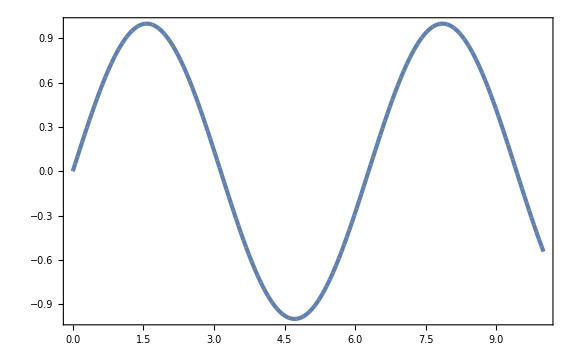

```mathematica
Show[ListPlot[xList],Plot[Sin[x],{x,0,10},PlotStyle->{Color[2],Dotted}]]
```

## NoiseMap

```mathematica
NoiseMapData=Import["NoiseMap.dat"];
```

```mathematica
num=Length[NoiseMapData]^(1/3);
```

```mathematica
deltaN=Table[Table[Table[NoiseMapData[[num^2 (nz-1)+num(ny-1)+nx,1]],{nx,num}],{ny,num}],{nz,num}];
```

```mathematica
ListDensityPlot3D[deltaN,BoxRatios->{1, 1, 1},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[deltaN[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
(*ζt=0 klist;ζe=Table[{0},{ksize}];
Do[Do[If[norm3[nx,ny,nz]≥klist[[ii]],If[norm3[nx,ny,nz]<klist[[ii+1]],{ζtemp=Abs[ζk[nx,ny,nz]]^2;ζt[[ii]]+=ζtemp;ζe[[ii]]=Join[ζe[[ii]],{ζtemp}];}]],{nz,num},{ny,num},{nx,num}],{ii,ksize}]//AbsoluteTiming*)
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=ParallelTable[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{23.357,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

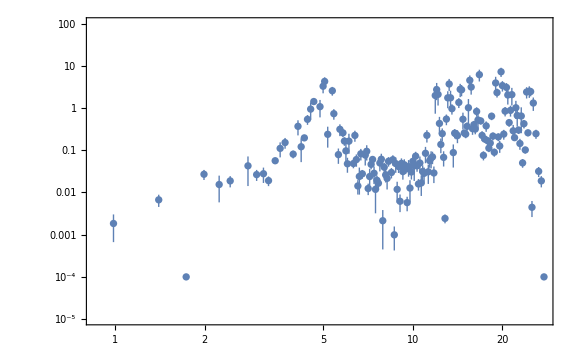

```mathematica
ListLogLogPlot[taberr,PlotRange->(*All*){10^-5,10^2},Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatdN=deltaN//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatdN]
```

1.05293

```mathematica
ck Total[ζt]/(num^3 ck)
```

1.05275